```mathematica
2+2
```

4

```mathematica
4+4
```

8

```mathematica
G = Exp[1]
```

ⅇ

```mathematica
G
```

ⅇ

```mathematica
G+2
```

2+ⅇ

```mathematica
G/e
```

ⅇ/e

```mathematica
g/E
```

g/ⅇ

```mathematica
G/E
```

1

```mathematica
D[Sin[x],x]
```

```mathematica
Cos[x]
```

Cos[x]

```mathematica
D[x^2 + 3x, x]
```

3+2 x



```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Decrecimiento[x_]:=Exp[-0.5x]*Sin[50*x]
```

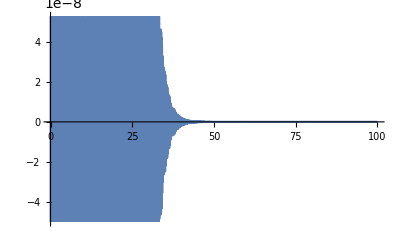

```mathematica
Plot[Decrecimiento[x],{x, 0,100}]
```

```mathematica
D[x^2 + 500x,x]
```

500+2 x

```mathematica
(7>6)&&(3==7)
```

False

```mathematica
Funcion[x_] = 3*x + 5
if[(2 > 1), Print["Se cumple"]]
```

5+3 x

Se cumple

if[True,Null]

```mathematica
array1 = {{1,2},{2,4},{3,6},{4,8}}
```

{{1,2},{2,4},{3,6},{4,8}}

```mathematica
array1
```

{{1,2},{2,4},{3,6},{4,8}}

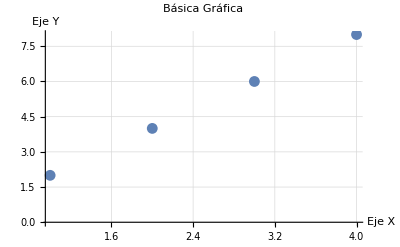

```mathematica
ListPlot[array1, PlotLabel->Gráfica Básica, GridLines->Automatic, AxesLabel->{"Eje X", "Eje Y"}] (*Graficación básica*)
```

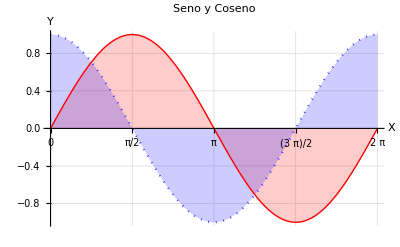

```mathematica
Plot[{Sin[x],Cos[x]}, {x,0,2Pi}, PlotLabel->"Seno y Coseno", AxesLabel->{"X","Y"}, Filling->Axis, PlotStyle->{{Red, Thick}, {Blue, Dotted}}, Ticks->{{0, Pi/2,Pi,3Pi/2, 2Pi}, Automatic}, TicksStyle->Directive[Black, Thick, Bold], GridLines->Automatic, GridLinesStyle->Directive[Dotted, Gray]]
(*Aquí se grafican varias funciones y se sombre el área bajo la curva. Se aplican también distintos tipos de línea a las dos gráficas.*)
(*Se incluye también manejo de los labels de los ejes.*)
```